(0.6 w | ⅈ k | 3 ⅈ w | 0
-ⅈ k | 0.6 w | 0 | 3 ⅈ w
-3 ⅈ w | 0 | 0.6 w | ⅈ k
0 | -3 ⅈ w | -ⅈ k | 0.6 w)

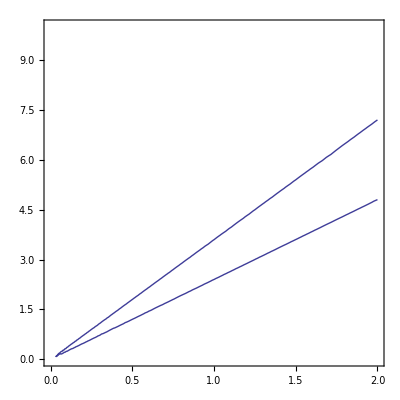

-Graphics3D-

-Graphics-

```mathematica
ClearAll["Global`*"]
epi:=3
mu:=3
r:=.6
i:=I
b:=2*Pi
S1:={w r ,i k , i w mu ,0};
S2:={-i k , w r ,0,i w mu};
S3:={- i w epi,0,w r ,i k };
S4:={0, -i w epi ,-i k ,w  r};
S:={S1,S2,S3,S4};
S//MatrixForm
s:=Det[S]
wa:=0
wb:=2
ka:=0
kb:=10
ContourPlot[s==0,{w,wa,wb},{k,ka,kb}] 
p1=Plot3D[s,{w,wa,wb},{k,ka,kb} ];
p2=Plot3D[0,{w,wa,wb},{k,ka,kb}];
Show[p1,p2,PlotRange->{-.001,.001}](*a3,a5,a9,a11 case*)

T1:={w r ,-i k , i w mu,0}
T2:={i k,w r,0,i w mu}
T3:={-i w epi,0,w r,-i k }
T4:={0 ,-i w epi,i k, w r}
T:={T1,T2,T3,T4}
T//MatrixForm;
t:=Det[T]
ContourPlot[t==0,{w,wa,wb},{k,ka,kb}]
```